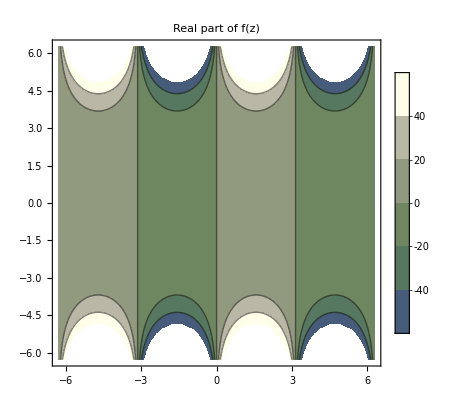

```mathematica
f[z_]:=Sin[z]  

ContourPlot[Re[f[x+I y]],{x,-2 π,2 π},{y,-2 π,2 π},ColorFunction-> "AlpineColors",PlotLegends->Automatic,PlotLabel->"Real part of f(z)"]
```

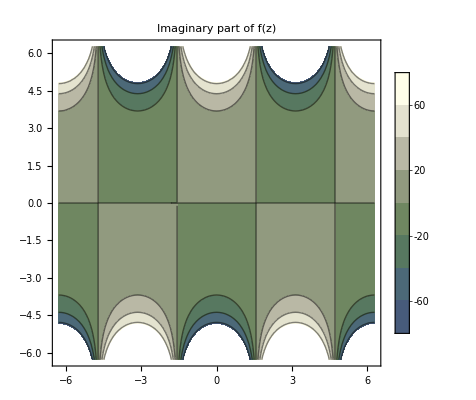

```mathematica
ContourPlot[Im[f[x+I y]],{x,-2 π,2 π},{y,-2 π,2 π},ColorFunction-> "AlpineColors",PlotLegends->Automatic,PlotLabel->"Imaginary part of f(z)"]
```

```mathematica
couchyRiemannEquation = {D[u[x,y], x] == D[v[x,y], y], D[u[x,y], y] == -D[v[x,y], x], u[x,0] == f[x], v[x,0] == 0}
```

{u^(1,0)[x,y]==v^(0,1)[x,y],u^(0,1)[x,y]==-v^(1,0)[x,y],u[x,0]==Sin[x],v[x,0]==0}

```mathematica
couchyRiemannDSolve = DSolve[couchyRiemannEquation, {u,v}, {x,y}]
```

{{u→Function[{x,y},Cosh[y] Sin[x]],v→Function[{x,y},Cos[x] Sinh[y]]}}

```mathematica
{reals, imaginary} = {u,v}/.couchyRiemannDSolve[[1]];
```

```mathematica
FullSimplify[reals[x,y] + I imaginary[x,y] == f[x + I y], x ∈ Reals | y ∈ Reals]
```

True